## Page-Wootters model: NN-level clock + 2-level system

```mathematica
NN= 32
```

32

```mathematica
T := DiagonalMatrix[Range[0,NN-1]]
```

```mathematica
MatrixForm[T]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 25 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 31)

```mathematica
F := FourierMatrix[NN]
```

```mathematica
Ω := F.T.F†
```

Hamiltonian in "ordinary" space

```mathematica
Hs := ⅈ{{0,1},{-1,0}}
```

```mathematica
MatrixForm[Hs]
```

(0 | ⅈ
-ⅈ | 0)

```mathematica
TeXForm[Hs]
```

"\\left(\n\\begin{array}{cc}\n 0 & i \\\\\n -i & 0 \\\\\n\\end{array}\n\\right)"

Matrix representation of eq. (1) in https://arxiv.org/abs/1504.04215 by Lloyd, Giovannetti and Maccone.
We turn it into numeric as treating  it symbolically onwards would be unfeasible.

```mathematica
J := N[KroneckerProduct[Ω,IdentityMatrix[2]] + KroneckerProduct[IdentityMatrix[NN],Hs]]
```

```mathematica
Chop[Eigenvalues[J]]
```

{32.,31.,30.,30.,29.,29.,28.,28.,27.,27.,26.,26.,25.,25.,24.,24.,23.,23.,22.,22.,21.,21.,20.,20.,19.,19.,18.,18.,17.,17.,16.,16.,15.,15.,14.,14.,13.,13.,12.,12.,11.,11.,10.,10.,9.,9.,8.,8.,7.,7.,6.,6.,5.,5.,4.,4.,3.,3.,2.,2.,1.,1.,-1.,0}

```mathematica
Eigenvalues[J][[40]]
```

12.

```mathematica
Eigenvalues[J][[41]]
```

11.

```mathematica
chosenEigenvector := Eigenvectors[J][[ 40]]

chosenEigenvectorB := Eigenvectors[J][[41]]

chosenProbUnnormalized := Abs[chosenEigenvector^2]
chosenProbUnnormalizedB := Abs[chosenEigenvectorB^2]
```

```mathematica
Normalization := chosenProbUnnormalized[[1]] + chosenProbUnnormalized[[2]]
```

```mathematica
NormalizationB := chosenProbUnnormalizedB[[1]] + chosenProbUnnormalizedB[[2]]
```

```mathematica
probability := chosenProbUnnormalized / Normalization
```

```mathematica
probabilityB := chosenProbUnnormalizedB/ NormalizationB
```

```mathematica
probability
```

{0.716702,0.283298,0.771924,0.228076,0.785749,0.214251,0.756071,0.243929,0.687408,0.312592,0.590214,0.409786,0.479286,0.520714,0.371512,0.628488,0.283298,0.716702,0.228076,0.771924,0.214251,0.785749,0.243929,0.756071,0.312592,0.687408,0.409786,0.590214,0.520714,0.479286,0.628488,0.371512,0.716702,0.283298,0.771924,0.228076,0.785749,0.214251,0.756071,0.243929,0.687408,0.312592,0.590214,0.409786,0.479286,0.520714,0.371512,0.628488,0.283298,0.716702,0.228076,0.771924,0.214251,0.785749,0.243929,0.756071,0.312592,0.687408,0.409786,0.590214,0.520714,0.479286,0.628488,0.371512}

```mathematica
probabilityB
```

{0.881533,0.118467,0.744511,0.255489,0.570264,0.429736,0.38532,0.61468,0.217835,0.782165,0.0933066,0.906693,0.0306941,0.969306,0.0395291,0.960471,0.118467,0.881533,0.255489,0.744511,0.429736,0.570264,0.61468,0.38532,0.782165,0.217835,0.906693,0.0933066,0.969306,0.0306941,0.960471,0.0395291,0.881533,0.118467,0.744511,0.255489,0.570264,0.429736,0.38532,0.61468,0.217835,0.782165,0.0933066,0.906693,0.0306941,0.969306,0.0395291,0.960471,0.118467,0.881533,0.255489,0.744511,0.429736,0.570264,0.61468,0.38532,0.782165,0.217835,0.906693,0.0933066,0.969306,0.0306941,0.960471,0.0395291}

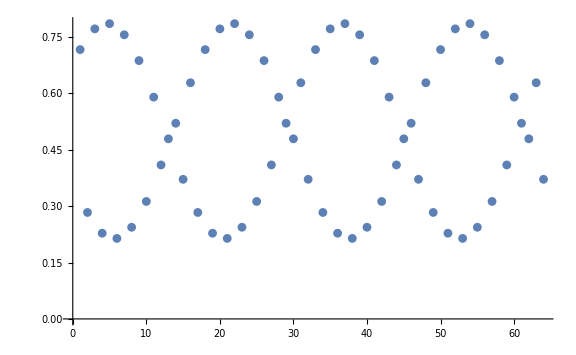

```mathematica
ListPlot[probability, GridLines ->{Range[0,NN*2, 2], Range[0,1,0.1]}, ImageSize->Large]
```

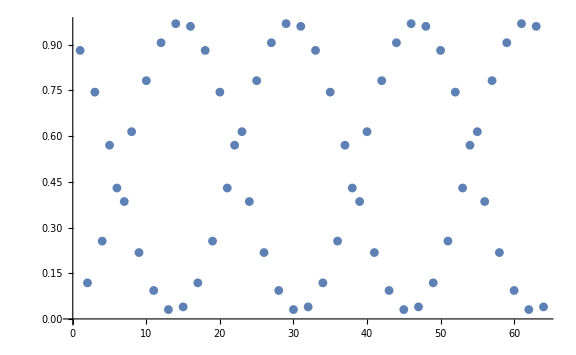

```mathematica
ListPlot[probabilityB, GridLines ->{Range[0,NN*2, 2], Range[0,1,0.1]}, ImageSize->Large]
```

Consistency of PW with ordinary QM (discrete approximation):

Ordinary quantum mechanics time evolution, with initial state  (1-i)/2 * |0>  + (1+i)/2 |1>

```mathematica
psi[t_] := MatrixExp[-ⅈ Hs t, {(1/2)-(1/2)ⅈ,(1/2)+(1/2)ⅈ} ]
```

```mathematica
psi[t]
```

{(1/2-ⅈ/2) Cos[t]+(1/2+ⅈ/2) Sin[t],(1/2+ⅈ/2) Cos[t]-(1/2-ⅈ/2) Sin[t]}

Picking 8 samples, equally spaced from 0 to 2π (excluding 2π)

```mathematica
Map[psi, Range[0,(7/4)π,π/4]]
```

{{1/2-ⅈ/2,1/2+ⅈ/2},{1/(√2),ⅈ/(√2)},{1/2+ⅈ/2,-1/2+ⅈ/2},{ⅈ/(√2),-1/(√2)},{-1/2+ⅈ/2,-1/2-ⅈ/2},{-1/(√2),-ⅈ/(√2)},{-1/2-ⅈ/2,1/2-ⅈ/2},{-ⅈ/(√2),1/(√2)}}

This discrete time evolution (samples from an ordinary QM result) coincides with the eigenvector of J related to eigenvalue 0 (PW model result).

```mathematica
Eigensystem[Hs]
```

{{-1,1},{{-ⅈ,1},{ⅈ,1}}}

```mathematica
Export["pwn.tex", "tex"]
```

pwn.tex

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["pwn.tex"]]]
```